```mathematica
readLog[path_]:=Module[{data},
data=ToExpression/@(Import[path]//StringSplit[#,"\n"]&);
#⟦All,{2,3}⟧&/@GroupBy[data,First]]
```

```mathematica
runningAvg[xs_,alpha_]:=
FoldList[
Function[
{old,new},
old*(1-alpha)+alpha*new
],
First[xs],
Drop[xs,1]
]
```

```mathematica
smoothCurve[points_,alpha_]:={points⟦All,1⟧,runningAvg[points⟦All,2⟧,alpha]}ᵀ
```

```mathematica
drawSingleCurve[name_,data_,alpha_,options_]:=Module[
{points=data⟦name⟧},
ListPlot@@(
{{Tooltip[smoothCurve[points,alpha],name],points},
PlotLabel->name,
Joined->True,
Filling->{2->{{1},Directive[RGBColor[0.990417, 0.500267, 0.0328679,0.3]]}},
PlotStyle->{Orange,Transparent},
PlotRange->All}~Join~options)]
```

```mathematica
drawMultipleCurves[plotName_,names_List,data_,alpha_,options_]:=Module[
{curves},
curves=Table[Tooltip[smoothCurve[data⟦n⟧,alpha],n],{n,names}];
ListPlot@@(
{curves,
PlotLabel->plotName,
Joined->True,
PlotLegends->Placed[names,Below],
PlotRange->All}~Join~options)]
```

```mathematica
drawBarChar[name_,data_,options_]:=
With[
{points=data⟦name⟧},
If[Length[points]==0,
"Need more data",
Manipulate[
Module[
{distr=points⟦epoch,2⟧},
BarChart@@({distr⟦All,2⟧,ChartLabels->distr⟦All,1⟧}~Join~options)
],
{{epoch,Length[points]},1,Length[points],1}]
]
]
```

```mathematica
drawAll[path_]:=Module[{data,lossGraph,trainAccGraph,distAccGraph,testAccGraph,timeGraph},
data=readLog[path];
lossGraph=drawSingleCurve["loss",data,0.2,{ImageSize->Medium}];
trainAccGraph=drawMultipleCurves["accuracies",{"libAcc","projAcc"},data,0.3,{ImageSize->Medium}];
testAccGraph=drawMultipleCurves["test accuracies",{"test-libAcc","test-projAcc"},data,1.0,{ImageSize->Medium}];
timeGraph=drawSingleCurve["iter-time",data,0.1,{ImageSize->Medium}];
distAccGraph=drawBarChar["distanceAcc",data,{ImageSize->Medium,PlotLabel->"Accuracy vs Distance"}];
Row[{lossGraph,trainAccGraph,testAccGraph,timeGraph,distAccGraph}]
]
```

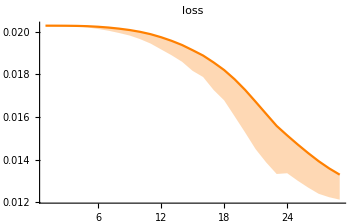
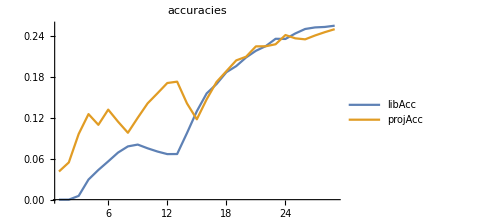
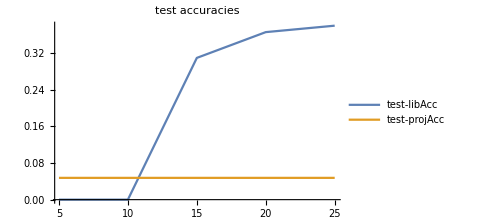
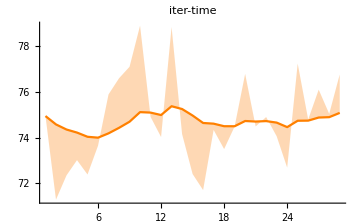

```mathematica
SetDirectory[NotebookDirectory[]];
drawAll["../running-result/log.txt"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
test=readLog["../running-result/log.txt"]
```

<|loss→{{1,0.0202748},{2,0.0202696}},libAcc→{{1,0.},{2,0.}},projAcc→{{1,0.0411392},{2,0.085443}},distanceAcc→{{1,{{1,0.00552486},{2,0.0166667},{3,0.0347826},{4,0.},{5,0.},{6,0.},{Inf,0.0109409}}},{2,{{1,0.00552486},{2,0.0277778},{3,0.0434783},{4,0.0571429},{5,0.},{6,0.},{Inf,0.0306346}}}},iter-time→{{1,74.947},{2,71.2827}}|>

```mathematica
Dynamic[display]
```

```mathematica
stopAll[];
SetDirectory[NotebookDirectory[]];
RunScheduledTask[
display=drawAll["../running-result/log.txt"];
Print["Redraw:"<> ToString[Now[]]],
{2,3000}];
```

```mathematica
stopAll[]
```

{}

```mathematica
(*Draw log from the server*)
Run["cd ~/Desktop;scp utopia2:~/TypingNet/running-result/log.txt running/log.txt"];
Run["cd ~/Desktop;scp utopia2:~/TypingNet/console.txt running/console.txt"];
drawAll["/Users/weijiayi/Desktop/running/log.txt"]
```